```mathematica
MyPower[p_,n_]:=MyPower[p,n] = p^n
```

```mathematica
Distance[n_,p_] := Module[ {threshold, digits, position, found, nextPower, result},
If [n ==0, Return[0]];
(* Initialize some precomputed local varables *)
threshold = (p-1)/2;
digits = IntegerDigits[n,p];

(* find the first digit above the threshold *)
found = -1;
For[ position = 1, position <=Length[digits], position++,
If [ digits [[position]] > threshold,
found = position; Break[]
]
];

(* if we didn't find a digit, then the distance is zero *)
If [found ==-1, Return[0]];

(* we did find a faulty digit.  Now we need to look before it for digits that equal the threshold.
If we would not coun these then we would end up with a new value which is still not p-good (due
to the carrying) *)
While[ found >1,
If [ digits [[found-1]] == threshold,found --,Break[]]
];

(* if we have gone all the way to the start*)
If[found ==1,
Block[{},
nextPower= MyPower[p,(Length[digits])];
Return[nextPower-n]
]
];


nextPower=MyPower[ p,(Length[digits]+1-found)];
Return[nextPower-FromDigits[Take[digits,-(Length[digits]+1-found)],p]]
]
```

```mathematica
VerboseAlgoList[start_, end_, primes_] := Module[{result, current,  maxdist, distanceTable, currentLog, previousLog},
result = {};
current=start;
previousLog = 0;
While[current ≤ end,
(*Print[current];*)
distanceTable = ParallelTable[Distance[current, p], {p, primes}];
result = Append[result,{current,distanceTable}];
maxdist = Max[distanceTable];
If[maxdist==0,
current +=1;
,
current += maxdist;
];
currentLog = Floor[Log[10,current]];
If[currentLog > previousLog, PrintTemporary[StringJoin["current zone ", ToString[currentLog]]]];
previousLog = currentLog;
];
Return [result];
]
```

```mathematica
AlgoHistogram[start_,end_,primeList_] := With[{primes=_primeList},
With[
{data = VerboseAlgoList[start,end,primes]},
Histogram3D[
Table[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,data}],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of votes for " , ToString[primes]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left}
]
]
]
```

```mathematica
With[{primes={3,5,7,116447}},
With[
{data = VerboseAlgoList[0,10^1000,primes]},
Show[
ParallelTable[
ListPlot[
Table[{i,N[Log[data[[i]][[2]][[pPos]]+1]]}, {i,Length[data]}],
PlotLabel->StringJoin["Successive votes for " , ToString[primes]],
PlotStyle->Directive[ColorData["DarkRainbow"][1/pPos],Opacity[0.6]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"}
]
,{pPos, 1, Length[primes]}]
]
]
]
```

$Aborted

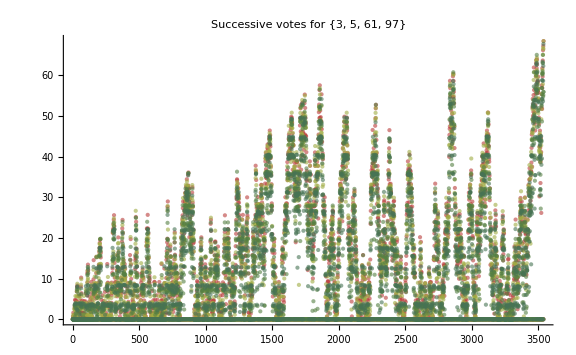

```mathematica
With[{primes={3,5,61,97}},
With[
{data = VerboseAlgoList[0,10^30,primes]},
Show[
ParallelTable[
ListPlot[
Table[{i,N[Log[data[[i]][[2]][[pPos]]+1]]}, {i,Length[data]}],
PlotLabel->StringJoin["Successive votes for " , ToString[primes]],
PlotStyle->Directive[ColorData["DarkRainbow"][1/pPos],Opacity[0.6]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"}
]
,{pPos, 1, Length[primes]}],
ImageSize->Large
]
]
]
```

```mathematica
With[{primes={31,37,59,79,89,97}},
With[
{data = VerboseAlgoList[0,10^100,primes]},
Histogram3D[
Table[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,data}],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of votes for " , ToString[primes]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left}
]
]
]
```

$Aborted

```mathematica
With[{primes={3}},
With[
{data = VerboseAlgoList[0,10^7,primes]},
Show[
ParallelTable[
ListPlot[
Table[{i,N[Log[data[[i]][[2]][[pPos]]+1]]}, {i,Length[data]}],
PlotLabel->StringJoin["Successive votes for " , ToString[primes]],
PlotStyle->Directive[ColorData["DarkRainbow"][1/pPos],Opacity[0.6]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"}
]
,{pPos, 1, Length[primes]}],
ImageSize->Large
]
]
]
```

$Aborted

```mathematica
With[{primes={3,5,7,11}},
With[
{data = VerboseAlgoList[0,10^2000,primes]},
Histogram3D[
Table[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,data}],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of votes for " , ToString[primes]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left}
]
]
]
```

-Graphics3D-

```mathematica
With[{primes={7,11,13,19}},
With[
{data = VerboseAlgoList[0,10^100,primes]},
Histogram3D[
Table[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,data}],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of votes for " , ToString[primes]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left}
]
]
]
```

-Graphics3D-

```mathematica
With[{primes={7,11,13,19}},
With[
{data = VerboseAlgoList[0,10^1000,primes]},
Histogram3D[
Table[Select[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,data}],#[[2]]>0&],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of votes for " , ToString[primes]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left},
ImageSize->Large
]
]
]
```

$Aborted

```mathematica
With[{primes={7,11,13,17}},
With[
{data = VerboseAlgoList[0,10^100,primes]},
Histogram3D[
Table[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,data}],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of votes for " , ToString[primes]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left}
]
]
]
```

-Graphics3D-

```mathematica
With[{primes={3,5,7,11}},
With[
{data = VerboseAlgoList[0,10^1000,primes]},
Histogram3D[
Table[Select[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,data}],#[[2]]>0&],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of votes for " , ToString[primes]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left},
ImageSize->Large
]
]
]
```

-Graphics3D-

```mathematica
With[{primes={7,11,13,19}},
With[
{data = VerboseAlgoList[0,10^100,primes]},
Histogram3D[
Table[Select[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,data}],#[[2]]>0&],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of votes for " , ToString[primes]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left},
ImageSize->Large
]
]
]
```

-Graphics3D-

```mathematica
With[{primes={7,11,13,17}},
With[
{data = VerboseAlgoList[0,10^100,primes]},
Histogram3D[
Table[Select[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,data}],#[[2]]>0&],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of votes for " , ToString[primes]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left},
ImageSize->Large
]
]
]
```

-Graphics3D-

```mathematica
With[{primes={7,11,13,17},
         rangeStart=10^90,
         rangeEnd = 10^110},
With[
{data = VerboseAlgoList[rangeStart,rangeEnd,primes]},
Histogram3D[
Table[Select[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,data}],#[[2]]>0&],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of votes for " , ToString[primes], " between 10^" ,ToString[ Log[10,rangeStart],StandardForm], " and 10^" , ToString[ Log[10,rangeEnd],StandardForm]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left},
ImageSize->Large
]
]
]
```

-Graphics3D-

```mathematica
Animate [
With[{primes={23,29,31,37},
         rangeStart=0,
         rangeEnd = 10^x},
With[
{data = VerboseAlgoList[rangeStart,rangeEnd,primes]},
Histogram3D[
Table[Select[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,data}],#[[2]]>0&],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of votes for " , ToString[primes], If[rangeStart==0," values up to 10^", StringJoin[" between 10^" ,ToString[ Log[10,rangeStart],StandardForm], " and 10^"]] , ToString[ Log[10,rangeEnd],StandardForm]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left},
ImageSize->Large
]
]
],
{x,1,10,1}
]
```

```mathematica
Table [
With[{primes={23,29,31,37},
         rangeStart=0,
         rangeEnd = 10^x},
With[
{data = VerboseAlgoList[rangeStart,rangeEnd,primes]},
Histogram3D[
Table[Select[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,data}],#[[2]]>0&],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of votes for " , ToString[primes], If[rangeStart==0," values up to 10^", StringJoin[" between 10^" ,ToString[ Log[10,rangeStart],StandardForm], " and 10^"]] , ToString[ Log[10,rangeEnd],StandardForm]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left},
ImageSize->Large
]
]
],
{x,1,10,1}
]
```

```mathematica
Export[
"jake.avi",
Table [
With[{primes={23,29,31,37},
         rangeStart=0,
         rangeEnd = 10^x},
With[
{data = VerboseAlgoList[rangeStart,rangeEnd,primes]},
Histogram3D[
Table[Select[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,data}],#[[2]]>0&],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of votes for " , ToString[primes], If[rangeStart==0," values up to 10^", StringJoin[" between 10^" ,ToString[ Log[10,rangeStart],StandardForm], " and 10^"]] , ToString[ Log[10,rangeEnd],StandardForm]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left},
ImageSize->Large
]
]
],
{x,1,10,1}
],
"Animation"]
```

jake.avi

```mathematica
Export[
"3-5-7-11.avi",
Block[{currentList={}},
Table [
PrintTemporary[x];

With[{primes={3,5,7,11},
         rangeStart=10^x-1,
         rangeEnd = 10^(x+1)},
With[
{data = VerboseAlgoList[rangeStart,rangeEnd,primes]},
currentList = Append[currentList, Flatten[data,1]];
Histogram3D[
Table[Select[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,currentList}],#[[2]]>0&],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of log of 'votes' for " , ToString[primes]," values up to 10^" , ToString[N[x+1],StandardForm]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left},
PerformanceGoal->"Quality"
]
]
],
{x,0,1000,1}
]
],
"Animation"]
```

3-5-7-11.avi

```mathematica
Export[
"3-5-7-11-running.avi",
Block[{currentList={}},
Table [
PrintTemporary[x];

With[{primes={3,5,7,11},
         rangeStart=10^x-1,
         rangeEnd = 10^(x+1)},
With[
{data = VerboseAlgoList[rangeStart,rangeEnd,primes]},
currentList = Append[currentList, data];
Print[currentList]
]
],
{x,2,10,1}
]
],
"Animation",
AnimationDisplayTime->3]
```

$Failed

```mathematica
Export[
"7-11-13-19.avi",
Block[{currentList={}},
Table [
PrintTemporary[x];

With[{primes={7,11,13,19},
         rangeStart=10^x-1,
         rangeEnd = 10^(x+1)},
With[
{data = VerboseAlgoList[rangeStart,rangeEnd,primes]},
currentList = Append[currentList, Flatten[data,1]];
Histogram3D[
Table[Select[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,currentList}],#[[2]]>0&],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of log of 'votes' for " , ToString[primes]," values up to 10^" , ToString[N[x+1],StandardForm]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left},
PerformanceGoal->"Quality"
]
]
],
{x,0,1000,1}
]
],
"Animation"]
```

```mathematica
Export[
"5-7-11.avi",
Block[{currentList={}},
Table [
PrintTemporary[x];

With[{primes={5,7,11},
         rangeStart=10^x-1,
         rangeEnd = 10^(x+1)},
With[
{data = VerboseAlgoList[rangeStart,rangeEnd,primes]},
currentList = Append[currentList, Flatten[data,1]];
Histogram3D[
Table[Select[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,currentList}],#[[2]]>0&],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of log of 'votes' for " , ToString[primes]," values up to 10^" , ToString[N[x+1],StandardForm]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left},
PerformanceGoal->"Quality"
]
]
],
{x,0,20,1}
]
],
"Animation"]
```

5-7-11.avi

```mathematica
With[{primes={7,11,13,17},
         rangeStart=0,
         rangeEnd = 10^200},
With[
{data = VerboseAlgoList[rangeStart,rangeEnd,primes]},
Histogram3D[
Table[Select[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,data}],#[[2]]>0&],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of votes for " , ToString[primes], If[rangeStart==0," values up to 10^", StringJoin[" between 10^" ,ToString[ Log[10,rangeStart],StandardForm], " and 10^"]] , ToString[ Log[10,rangeEnd],StandardForm]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left},
ImageSize->Large
]
]
]
```

-Graphics3D-

```mathematica
With[{primes={7,11,13,19},
         rangeStart=0,
         rangeEnd = 10^200},
With[
{data = VerboseAlgoList[rangeStart,rangeEnd,primes]},
Histogram3D[
Table[Select[Table[{i,N[Log[(n[[2]][[i]]+1)]]},{n,data}],#[[2]]>0&],{i,1,Length[primes]}],
PlotLabel->StringJoin["Histogram of votes for " , ToString[primes], If[rangeStart==0," values up to 10^", StringJoin[" between 10^" ,ToString[ Log[10,rangeStart],StandardForm], " and 10^"]] , ToString[ Log[10,rangeEnd],StandardForm]],
LabelStyle->{FontSize->Larger, FontFamily->"Calibri"},
ViewPoint->{Back, Top,Left},
ImageSize->Large
]
]
]
```

-Graphics3D-